# Genetic Algorithm. Ex

## Dibuja la superficie y los valores de cada generación

```mathematica
life[e_,f_,{ax_,bx_},{ay_,by_}]:=Module[{n,ptos,graph},
		n=Length[e[[1,1]]];
		ptos=Table[Join[e[[i,1,j]],{e[[i,2,j]]}],{i,1,genera},{j,1,n}];
	ptos=Table[Map[Point,ptos[[i]]],{i,1,genera}];
		graph=Plot3D[Evaluate[f[{x,y}]],{x,ax,bx},{y,ay,by},Mesh->False,PlotPoints->25,DisplayFunction->Identity];
			Table[Show[graph,	
	Graphics3D[{PointSize[0.05],ptos[[i]]}],
ViewPoint->{1.290, -3.262, 1.850},DisplayFunction->$DisplayFunction,AspectRatio->Automatic],{i,1,genera}]
];
```

## Dibuja el mejor valor de cada Generacion

```mathematica
exhibit[matr_]:=Module[{n},
		n=Length[matr];
	ListPlot[{Table[Last[matr[[i,2]]],{i,1,n}],
				Table[matr[[i,3]],{i,1,n}]},
				Joined->True,Frame->True,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}]
				]
```

```mathematica
Programa del Algoritmo Genetico
```

```mathematica
GA[Fobjetive_,{ax_,bx_},{ay_,by_},prec_,popsize_,pcross_,pmuta_,generate_,sizesav_]:=
	Module[{
			pop={},generacN=0,
	  newpop={},fitness={},
			notification={},
		evolution={},xsize,ysize,chromsize,xfactor,
       yfactor,finx,iniy,finy,
			meanfit,maxfit,best},
(*tamaño de c/var y factor de conversión*)
Size[{a_,b_},pre_]:=Ceiling[Log[2,(b-a)*pre]];fac[larg_,m_]:=N[larg/(2^m-1)];
		(*inicializacion poblac*)
birth[psize_,chsize_]:=
Partition[Table[Random[Integer],{chsize*psize}],chsize];
		(*decodificacion: entra chromosoma y sale el individuo*)
decode[chrom_]:=Module[{xx,yy},
				decim[gen_]:=gen.Reverse[(2^(#-1))& /@  Range[Length[gen]]];	xx= ax+decim[Take[chrom,{1,finx}]]*xfactor ;
		       yy=ay+decim[Take[chrom,{iniy,finy}]]*yfactor ; 
		Return[List[xx,yy]]
			];
		          (*entra poblacion y sale lista: n mejores + sus ajustes + media geracional*)
			report[popul_,n_]:=Module[{majors,listfit,f,m,b},
					majors={decode[best]};
					listfit={maxfit};
					f=DeleteCases[fitness,maxfit];
					Do[m=Max[f];
						     b=First[Extract[popul,Position[f,m]]];
						    listfit=Join[{m},listfit];
						    majors=Join[{decode[b]},majors];
						   f=DeleteCases[f,m],
						{n-1}];
					meanfit=Plus@@fitness/popsize;
					Return[{majors,listfit,meanfit}]
				];
				(*Por el metodo "Remainder stochastic sampling with replacement"*)
	clones[popul_]:=Module [{ expected,remainder,acum,probwheel,wincopies,popaux},
		expected=fitness/meanfit ;
		popaux=Flatten[MapThread[Table[#1,{#2}]&,{popul,IntegerPart[expected]}],1];
	  probwheel=FractionalPart[ expected]/(Plus@@FractionalPart[expected]);
    acum=Rest[FoldList[Plus, 0.0, probwheel]];
    remainder=popsize-Length[popaux];
		wincopies=Table[(r=Random[]; i=1;Scan[If[#>r, Return[pop[[i]]], i++]&, acum]),
				{remainder}];
	 Flatten[List[popaux,wincopies],1]
		];
		(*entra poblac, se sortea segun pcross, los elegidos se aparean y se cruzan*)
		crossover[popnew_]:=Module[{mate,luck,children,popaux=popnew},	
		luck=Position[Table[Random[],{popsize}],r_/;r<pcross];
		If[OddQ[Length [luck]],luck=Rest[luck]];
		mate=Partition[Extract[popnew,luck],2];			
		children=Map[(j=Random[Integer,{1,(chromsize-1)}];
				List[Join[Take[#[[1]],j],Take[#[[2]],(j-chromsize)]],Join[Take[#[[2]],j],Take[#[[1]],(j-chromsize)]]])&,mate];
		children=Flatten[children,1];
		luck=Flatten[luck];
		Scan[(popaux[[luck[[#]]]]=children[[#]])& ,Range[Length[luck]]];
		Return[popaux]
		];
		(*Operador sobre los bits, y pmuta es deterministica*)
		mutation[popnew_]:=Module[{luck,tot=chromsize*popsize,popaux=popnew},
		luck=Table[Random[Integer,{1,tot}], {pmuta*tot}];
		popaux=Flatten[popaux];
		Scan[If[popaux[[#]]==0,popaux[[#]]=1,popaux[[#]]=0]&,luck];
		Return[Partition[popaux,chromsize]]		
		];		
		(* Main program *)	
      xsize=Size[{ax,bx},prec];
      ysize=Size[{ay,by},prec];
						chromsize=Plus@@{xsize,ysize};
       xfactor=fac[(bx-ax),xsize];
						yfactor=fac[(by-ay),ysize];
        finx=xsize; 
iniy=xsize+1;    finy=xsize+ysize;
		pop=birth[popsize,chromsize];
		generacN=1;
		While[generacN ≤ generate,
		Print[generacN];
	fitness=Map[Fobjetive[#]&,decode[#]&/@pop];
		maxfit=Max[fitness];
		best=First[Extract[pop,Position[fitness,maxfit]]];
         notification=report[pop,sizesav];
			(*Print[notification]*);
		evolution=Join[evolution,{notification}];
		newpop=clones[pop];
		newpop=crossover[newpop];
		newpop=mutation[newpop];
		(*elitismo*) 
		newpop[[1]]=best;
		pop=newpop;
		generacN++;
		newpop={};
];
Return[evolution]
]
```

## Ejemplo 1: escalonada

```mathematica
Fopt=Function[{u},-∑_(i=1)^2 Floor[u[[i]]]^2+50];
 rangoX={-5,5};
 rangoY={-5,5};
	 precis=10^3;
psize=15;
pcro=0.25;
pmu=0.1;
genera=10;
sizeSave=5;
```

```mathematica
ev=GA[Fopt,rangoX,rangoY,precis,psize,pcro,
	pmu,genera,sizeSave]
```

1

2

3

4

5

6

7

8

9

10

{{{{1.4103,-0.866447},{4.27608,-4.32308},{-1.7332,-4.76683},{1.4103,-0.866447},{1.01599,0.600928}},{41,45,46,48,49},527/15},{{{2.84167,-0.779161},{-2.73302,0.940304},{-4.08014,2.38815},{-2.73302,0.940304},{1.01599,0.600928}},{42,45,46,48,49},181/5},{{{3.24208,-2.02924},{1.14417,0.940914},{-1.05323,4.48788},{2.9552,0.776109},{1.01599,0.600928}},{42,45,46,48,49},110/3},{{{1.01599,0.600928},{-2.72996,1.09656},{2.84167,-0.779161},{2.87707,0.737044},{1.01599,0.600928}},{40,45,46,48,49},539/15},{{{1.16371,2.27889},{1.01599,0.600928},{-2.72996,1.09412},{1.01599,0.600928},{0.376915,0.733993}},{33,40,45,49,50},587/15},{{{-3.97027,1.09656},{1.16371,2.20076},{-3.97027,1.09656},{0.376915,0.733993},{0.376915,0.733993}},{40,42,45,49,50},614/15},{{{1.15394,2.20076},{0.376305,1.98407},{0.376915,0.733993},{1.15394,2.20076},{0.376915,0.733993}},{41,42,45,49,50},641/15},{{{-0.374474,4.38595},{0.376915,0.733993},{-0.374474,4.38595},{2.2032,4.04901},{0.376915,0.733993}},{41,42,45,49,50},611/15},{{{0.13276,1.07215},{0.376915,0.733993},{3.22743,3.12244},{-3.52042,4.46042},{0.376915,0.733993}},{37,45,46,49,50},181/5},{{{1.30471,0.408655},{4.75768,1.57511},{4.75768,1.57511},{4.75768,1.57511},{0.376915,0.733993}},{41,45,46,49,50},622/15}}

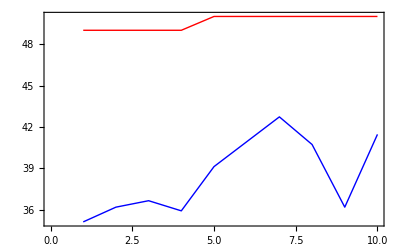

```mathematica
exhibit[ev]
```

```mathematica
life[ev,Fopt,rangoX,rangoY]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}